```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITX/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITX Price | % Change | log return future | log return BITX
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 49175.9 | 3.54% | 0.0212907 | 0.0347737
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 47495.3 | -14.92% | -0.0904653 | -0.161541
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 55822.2 | -0.76% | -0.0196938 | -0.00759423
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 56247.7 | -2.14% | -0.131645 | -0.142883
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 64887. | 6.13% | 0.03685 | 0.0594724
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 61140.6 | -11.16% | -0.119603 | -0.118361
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 68822.9 | -2.54% | -0.042369 | -0.0256963
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 70614.3 | 2.20% | 0.018947 | 0.021806
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 69091.2 | -1.10% | -0.0359909 | 0.0107786)

```mathematica
Dimensions[data]
```

{301,8}

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,8]]
```

log return BITX

```mathematica
data[[1,7]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=49, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data =   
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,7;;8⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{1.28713,0.115725}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_BITX/

```mathematica
For[kk=0, kk≤80, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,8⟧;
rf=data2⟦2;;All,7⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0710094 and 0.000109147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0703128 and 0.000101657 for the integral and error estimates.

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0700584 and 0.000106536 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.922771 | 0.743656 | 0.763593 | 0.611005 | 0.724686 | 0.754165
 | 2021-05-13 | 0.924155 | 0.752785 | 0.773987 | 0.677959 | 0.742117 | 0.736823
 | 2021-05-06 | 0.930785 | 0.768998 | 0.780767 | 0.700206 | 0.749792 | 0.754772
 | 2021-04-29 | 0.933969 | 0.773002 | 0.7812 | 0.705415 | 0.753645 | 0.768612
 | 2021-04-22 | 0.934478 | 0.774433 | 0.782571 | 0.707795 | 0.754855 | 0.769137
 | 2021-04-15 | 0.932814 | 0.776209 | 0.777066 | 0.704086 | 0.748282 | 0.769265
 | 2021-04-08 | 0.930346 | 0.770485 | 0.766304 | 0.702671 | 0.743383 | 0.763855
 | 2021-04-01 | 0.930811 | 0.771253 | 0.760593 | 0.706359 | 0.741984 | 0.760462
 | 2021-03-25 | 0.933278 | 0.782582 | 0.794159 | 0.702015 | 0.756472 | 0.774896
 | 2021-03-18 | 0.934695 | 0.780425 | 0.781988 | 0.707509 | 0.753107 | 0.770528
 | 2021-03-11 | 0.932716 | 0.77201 | 0.770393 | 0.705299 | 0.746686 | 0.765931
 | 2021-03-04 | 0.932739 | 0.775494 | 0.777753 | 0.70382 | 0.749616 | 0.769744
 | 2021-02-25 | 0.933624 | 0.786011 | 0.792456 | 0.705006 | 0.760762 | 0.780135
 | 2021-02-18 | 0.931308 | 0.776037 | 0.776726 | 0.706686 | 0.741799 | 0.773146
 | 2021-02-10 | 0.934558 | 0.782483 | 0.78609 | 0.711845 | 0.74942 | 0.779436
 | 2021-02-03 | 0.93587 | 0.786529 | 0.790773 | 0.718156 | 0.755655 | 0.77828
 | 2021-01-27 | 0.939151 | 0.803401 | 0.827196 | 0.714978 | 0.77283 | 0.795471
 | 2021-01-20 | 0.94083 | 0.814829 | 0.834255 | 0.72288 | 0.775776 | 0.801181
 | 2021-01-12 | 0.936154 | 0.806595 | 0.803632 | 0.718557 | 0.761483 | 0.788205
 | 2021-01-05 | 0.93905 | 0.79391 | 0.820574 | 0.717983 | 0.762102 | 0.810022
 | 2020-12-28 | 0.935089 | 0.778565 | 0.799916 | 0.716196 | 0.750858 | 0.79318
 | 2020-12-18 | 0.939732 | 0.797026 | 0.832659 | 0.726089 | 0.769156 | 0.806568
 | 2020-12-11 | 0.936221 | 0.788703 | 0.806914 | 0.725549 | 0.759196 | 0.785803
 | 2020-12-04 | 0.935437 | 0.788169 | 0.805569 | 0.724709 | 0.758119 | 0.784986
 | 2020-11-27 | 0.933784 | 0.808035 | 0.802072 | 0.727913 | 0.760806 | 0.762219
 | 2020-11-19 | 0.944341 | 0.834304 | 0.820922 | 0.757652 | 0.782814 | 0.791569
 | 2020-11-12 | 0.942607 | 0.830561 | 0.819288 | 0.754423 | 0.779999 | 0.786453
 | 2020-11-05 | 0.943915 | 0.836794 | 0.817407 | 0.756587 | 0.778132 | 0.793754
 | 2020-10-29 | 0.944137 | 0.836659 | 0.817309 | 0.756357 | 0.778815 | 0.791903
 | 2020-10-22 | 0.942671 | 0.827593 | 0.807718 | 0.756145 | 0.773624 | 0.782237
 | 2020-10-15 | 0.942633 | 0.826975 | 0.816738 | 0.754963 | 0.775389 | 0.778549
 | 2020-10-08 | 0.942297 | 0.824479 | 0.809778 | 0.752237 | 0.770749 | 0.786569
 | 2020-10-01 | 0.942331 | 0.823871 | 0.809778 | 0.750458 | 0.769372 | 0.787835
 | 2020-09-24 | 0.942197 | 0.823555 | 0.808719 | 0.752377 | 0.769293 | 0.78376
 | 2020-09-17 | 0.942464 | 0.81487 | 0.804805 | 0.75125 | 0.771976 | 0.779138
 | 2020-09-10 | 0.948396 | 0.822927 | 0.816411 | 0.754012 | 0.782698 | 0.797791
 | 2020-09-02 | 0.953271 | 0.847647 | 0.853613 | 0.766437 | 0.823061 | 0.819703
 | 2020-08-26 | 0.949804 | 0.819247 | 0.802856 | 0.755642 | 0.790507 | 0.806473
 | 2020-08-19 | 0.948783 | 0.80198 | 0.785946 | 0.755678 | 0.783022 | 0.802502
 | 2020-08-12 | 0.947326 | 0.797523 | 0.781921 | 0.755225 | 0.779599 | 0.798985
 | 2020-08-05 | 0.947864 | 0.806267 | 0.797887 | 0.7484 | 0.790873 | 0.803012
 | 2020-07-29 | 0.953596 | 0.820659 | 0.808238 | 0.761646 | 0.801379 | 0.816394
 | 2020-07-22 | 0.955387 | 0.824954 | 0.832677 | 0.76556 | 0.807809 | 0.817628
 | 2020-07-15 | 0.954456 | 0.820184 | 0.83259 | 0.758182 | 0.804087 | 0.824155
 | 2020-07-08 | 0.952672 | 0.814304 | 0.824887 | 0.748104 | 0.797794 | 0.820748
 | 2020-06-30 | 0.951723 | 0.794411 | 0.814453 | 0.74608 | 0.790183 | 0.814903
 | 2020-06-23 | 0.949752 | 0.7954 | 0.810683 | 0.740795 | 0.786445 | 0.8119
 | 2020-06-16 | 0.950469 | 0.790376 | 0.812525 | 0.744422 | 0.783715 | 0.810488
 | 2020-06-09 | 0.949745 | 0.775777 | 0.799213 | 0.744612 | 0.774556 | 0.808379
 | 2020-06-02 | 0.94963 | 0.774507 | 0.798484 | 0.744203 | 0.774223 | 0.807734
 | 2020-05-26 | 0.949653 | 0.774333 | 0.798785 | 0.745542 | 0.774327 | 0.80735
 | 2020-05-18 | 0.947344 | 0.769131 | 0.793912 | 0.743015 | 0.768626 | 0.801514
 | 2020-05-11 | 0.945023 | 0.764545 | 0.793707 | 0.734916 | 0.764962 | 0.797602
 | 2020-05-04 | 0.942692 | 0.76668 | 0.775516 | 0.742982 | 0.758141 | 0.790648
 | 2020-04-27 | 0.944343 | 0.773937 | 0.781441 | 0.748353 | 0.764725 | 0.790549
 | 2020-04-20 | 0.944292 | 0.771044 | 0.787804 | 0.741977 | 0.763981 | 0.78972
 | 2020-04-13 | 0.941645 | 0.768127 | 0.774444 | 0.746479 | 0.758536 | 0.784821
 | 2020-04-03 | 0.940474 | 0.763274 | 0.761532 | 0.754118 | 0.75454 | 0.780875
 | 2020-03-27 | 0.939615 | 0.757124 | 0.785693 | 0.725035 | 0.754229 | 0.787656
 | 2020-03-20 | 0.937645 | 0.764065 | 0.773787 | 0.734304 | 0.752496 | 0.779499
 | 2020-03-13 | 0.935494 | 0.760299 | 0.775115 | 0.730142 | 0.75321 | 0.770657
 | 2020-03-06 | 0.941954 | 0.788954 | 0.774253 | 0.706854 | 0.743033 | 0.804281
 | 2020-02-28 | 0.940771 | 0.798446 | 0.787265 | 0.70801 | 0.749816 | 0.802749
 | 2020-02-21 | 0.940903 | 0.786344 | 0.746167 | 0.73128 | 0.740179 | 0.789422
 | 2020-02-13 | 0.942182 | 0.787966 | 0.776248 | 0.731166 | 0.743547 | 0.791215
 | 2020-02-06 | 0.945024 | 0.801669 | 0.821813 | 0.7151 | 0.760849 | 0.815326
 | 2020-01-30 | 0.948548 | 0.789298 | 0.769976 | 0.748958 | 0.762748 | 0.799336
 | 2020-01-23 | 0.944153 | 0.771711 | 0.769113 | 0.732667 | 0.760334 | 0.783492
 | 2020-01-15 | 0.941779 | 0.779279 | 0.80568 | 0.690721 | 0.763893 | 0.793114
 | 2020-01-08 | 0.935952 | 0.759937 | 0.77615 | 0.682758 | 0.746054 | 0.7755
 | 2019-12-31 | 0.932254 | 0.751185 | 0.778861 | 0.668412 | 0.740599 | 0.769031
 | 2019-12-23 | 0.927557 | 0.749258 | 0.791545 | 0.655479 | 0.7397 | 0.765286
 | 2019-12-16 | 0.929719 | 0.744913 | 0.77523 | 0.660136 | 0.734433 | 0.764351
 | 2019-12-09 | 0.928896 | 0.741763 | 0.775389 | 0.658049 | 0.734354 | 0.763329
 | 2019-12-02 | 0.927144 | 0.752949 | 0.793304 | 0.653293 | 0.739812 | 0.764856
 | 2019-11-22 | 0.925123 | 0.742493 | 0.792864 | 0.648476 | 0.736694 | 0.755537
 | 2019-11-15 | 0.91901 | 0.732403 | 0.760863 | 0.642082 | 0.720148 | 0.739596
 | 2019-11-08 | 0.920027 | 0.727571 | 0.731819 | 0.684012 | 0.717165 | 0.732031
 | 2019-11-01 | 0.922138 | 0.732403 | 0.735886 | 0.682344 | 0.719155 | 0.739212
 | 2019-10-25 | 0.921505 | 0.727571 | 0.738223 | 0.673822 | 0.716298 | 0.739221
 | 2019-10-18 | 0.920024 | 0.731745 | 0.725395 | 0.698307 | 0.720025 | 0.729714

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.956574 | 0.78657 | 0.792213 | 0.758085 | 0.792213 | 0.792619
 | 2021-05-13 | 0.833247 | 0.502919 | 0.531763 | 0.520713 | 0.528226 | 0.563372
 | 2021-05-06 | 0.869873 | 0.925606 | 0.938179 | 0.922685 | 0.938179 | -0.940328
 | 2021-04-29 | 0.697721 | 0.550471 | 0.486991 | 0.559169 | 0.469034 | 0.369281
 | 2021-04-22 | 0.955455 | 0.756237 | 0.771156 | 0.747979 | 0.773253 | 0.784675
 | 2021-04-15 | 0.935353 | 0.89197 | 0.917891 | 0.885205 | 0.914454 | -0.297312
 | 2021-04-08 | 0.965191 | 1.18571 | 1.13344 | 1.18571 | 1.15022 | 0.788271
 | 2021-04-01 | 0.951494 | 0.912274 | 0.957413 | 0.922662 | 0.946342 | 0.576398
 | 2021-03-25 | 0.951847 | -0.538509 | -0.877223 | -0.496959 | -0.862407 | 0.865141
 | 2021-03-18 | 0.973969 | 0.848713 | 0.850197 | 0.846986 | 0.850175 | 0.757798
 | 2021-03-11 | 0.956319 | 0.702082 | 0.718497 | 0.701849 | 0.716284 | 0.832432
 | 2021-03-04 | 0.747913 | 1.47319 | 1.62237 | 1.52193 | 1.60687 | 0.765498
 | 2021-02-25 | 0.972819 | 0.734297 | 0.754627 | 0.699715 | 0.748208 | 0.89004
 | 2021-02-18 | 0.988613 | 0.888978 | 0.914253 | 0.885346 | 0.915096 | 0.89401
 | 2021-02-10 | 0.788255 | 2.05415 | 2.12054 | 2.03118 | 2.11633 | 0.766309
 | 2021-02-03 | 0.900744 | 0.379058 | 0.210852 | 0.327275 | 0.211339 | 0.91513
 | 2021-01-27 | 0.839768 | -0.028705 | -0.283008 | 0.0736822 | -0.220247 | 0.861896
 | 2021-01-20 | 0.977088 | 0.924391 | 0.973103 | 0.893217 | 0.957392 | 0.630327
 | 2021-01-12 | 0.958033 | 0.984256 | 0.973458 | 0.982625 | 0.97583 | 0.597761
 | 2021-01-05 | 0.980496 | 0.900735 | 0.902021 | 0.900387 | 0.901741 | 0.791326
 | 2020-12-28 | 0.907533 | 3.40077 | 3.42975 | 2.85561 | 4.95457 | 0.783021
 | 2020-12-18 | 0.965167 | 0.101769 | 0.105079 | 0.101192 | 0.107883 | 0.939542
 | 2020-12-11 | 0.989726 | -5.68401 | -9.55835 | -5.68401 | -10.2267 | 0.997756
 | 2020-12-04 | 0.856085 | 0.648278 | 0.655824 | 0.647418 | 0.68945 | -0.477742
 | 2020-11-27 | 0.993178 | 0.755517 | 0.626799 | 0.727202 | 0.614157 | 0.980642
 | 2020-11-19 | 0.871357 | 0.807229 | 0.821737 | 0.799662 | 0.848946 | 0.0308563
 | 2020-11-12 | 0.934112 | 0.301887 | 0.185934 | 0.446829 | 0.191247 | 0.842104
 | 2020-11-05 | 0.847388 | -0.52722 | -0.755476 | -0.611264 | -0.718677 | 0.742094
 | 2020-10-29 | 0.979558 | -3.49779 | -4.76778 | -3.54552 | -4.40847 | 0.958068
 | 2020-10-22 | 0.992043 | 0.797014 | 0.770447 | 0.771204 | 0.764836 | 1.05926
 | 2020-10-15 | 0.949433 | 0.472266 | 0.418032 | 0.432962 | 0.424994 | 0.886232
 | 2020-10-08 | 0.9764 | 0.753282 | 0.763479 | 0.760992 | 0.763313 | 0.864069
 | 2020-10-01 | 0.976418 | 0.672848 | 0.706104 | 0.694922 | 0.705441 | 0.915543
 | 2020-09-24 | 0.952015 | 0.752185 | 0.799954 | 0.785737 | 0.798667 | 0.689499
 | 2020-09-17 | 0.953847 | 0.68848 | 0.736317 | 0.742298 | 0.732999 | 0.859129
 | 2020-09-10 | 0.182227 | 4.32002 | 4.51147 | 4.39293 | 4.55061 | 0.534725
 | 2020-09-02 | 0.947382 | 0.715129 | 0.724961 | 0.704051 | 0.728344 | 0.792479
 | 2020-08-26 | 0.933797 | 0.813157 | 0.833611 | 0.863205 | 0.838547 | 0.535269
 | 2020-08-19 | 0.957426 | 0.82472 | 0.825663 | 0.844953 | 0.832919 | 0.704436
 | 2020-08-12 | 0.927983 | 0.642655 | 0.669124 | 0.69863 | 0.672852 | 0.670392
 | 2020-08-05 | 0.987187 | 0.871119 | 0.887698 | 0.918088 | 0.893748 | 0.842535
 | 2020-07-29 | 0.420562 | 0.621507 | 0.520294 | 0.505897 | 0.567035 | 0.0958252
 | 2020-07-22 | 0.971182 | 8.70567 | 17.0037 | 18.288 | 13.6789 | 0.884535
 | 2020-07-15 | 0.936292 | 0.592754 | 0.603084 | 0.591126 | 0.604095 | 0.842606
 | 2020-07-08 | 0.972802 | 0.906256 | 0.962262 | 0.959758 | 0.945782 | 0.458032
 | 2020-06-30 | 0.978962 | 1.08494 | 1.06242 | 1.05513 | 1.06069 | 0.707775
 | 2020-06-23 | 0.955083 | 0.826413 | 0.835026 | 0.836249 | 0.835353 | 2.2381
 | 2020-06-16 | 0.990289 | 0.899472 | 0.975536 | 0.955383 | 0.960361 | 0.874169
 | 2020-06-09 | 0.996523 | 0.911352 | 0.948931 | 0.948942 | 0.948526 | 0.950727
 | 2020-06-02 | 0.961598 | 0.725601 | 0.458869 | 0.457491 | 0.517055 | 0.880104
 | 2020-05-26 | 0.923374 | 0.35855 | 0.488323 | 0.40728 | 0.498815 | 0.713911
 | 2020-05-18 | 0.968327 | 0.956458 | 0.945082 | 0.954606 | 0.938728 | 0.443679
 | 2020-05-11 | 0.985163 | 0.878997 | 0.912935 | 0.906158 | 0.920231 | 0.851589
 | 2020-05-04 | 0.992865 | 0.917934 | 0.927409 | 0.922527 | 0.933616 | 0.905115
 | 2020-04-27 | 0.986011 | 0.260426 | 0.270763 | 0.260426 | 0.281721 | 0.939807
 | 2020-04-20 | 0.946077 | 4.63976 | 4.44015 | 4.39301 | 3.69994 | 0.869787
 | 2020-04-13 | 0.994624 | 0.874116 | 0.948492 | 0.957453 | 0.944289 | 0.921738
 | 2020-04-03 | 0.987796 | 0.979741 | 0.947596 | 0.97905 | 0.945883 | 0.881092
 | 2020-03-27 | 0.986146 | 0.87441 | 0.690862 | 0.719061 | 0.740259 | 0.920768
 | 2020-03-20 | 0.989783 | 0.713772 | 0.74391 | 0.739932 | 0.742292 | 0.953574
 | 2020-03-13 | 0.986763 | 0.701789 | 0.77413 | 0.770501 | 0.768256 | 0.989575
 | 2020-03-06 | 0.981402 | 0.869707 | 0.924186 | 0.874607 | 0.909836 | -0.478009
 | 2020-02-28 | 0.972078 | 0.715978 | 0.77731 | 0.714504 | 0.744473 | 0.876411
 | 2020-02-21 | 0.902148 | 0.721343 | 0.730416 | 0.734379 | 0.733838 | 0.357675
 | 2020-02-13 | 0.966831 | 0.853632 | 0.877421 | 0.881527 | 0.883012 | 0.74519
 | 2020-02-06 | 0.906655 | 1.1528 | 1.07977 | 1.15281 | 1.17865 | 0.60824
 | 2020-01-30 | 0.935338 | 0.651472 | 0.69607 | 0.686038 | 0.680054 | 0.7469
 | 2020-01-23 | 0.967776 | 1.25815 | 1.30846 | 1.35415 | 1.33336 | 0.916664
 | 2020-01-15 | 0.967767 | 0.803451 | 0.881098 | 0.797283 | 0.836535 | 0.724283
 | 2020-01-08 | 0.973747 | 0.999503 | 1.04873 | 1.02573 | 1.04434 | 0.82156
 | 2019-12-31 | 0.948403 | 0.653277 | 0.536587 | 0.698032 | 0.609466 | 0.81025
 | 2019-12-23 | 0.862358 | 0.770702 | 0.764144 | 0.771256 | 0.767448 | 0.277182
 | 2019-12-16 | 0.982245 | 0.721443 | 0.78054 | 0.732089 | 0.745662 | 0.971108
 | 2019-12-09 | 0.968612 | 0.799316 | 0.860859 | 0.806954 | 0.826781 | 0.726449
 | 2019-12-02 | 0.988761 | 1.00021 | 0.847561 | 0.959138 | 0.938003 | 0.855197
 | 2019-11-22 | 0.988732 | 0.875939 | 0.859907 | 0.859185 | 0.887525 | 0.938081
 | 2019-11-15 | 0.996227 | 0.94188 | 0.97382 | 0.903577 | 0.948982 | 1.53731
 | 2019-11-08 | 0.887189 | 0.885126 | 0.854253 | 0.874995 | 0.872242 | -0.218032
 | 2019-11-01 | 0.974299 | 0.952293 | 0.956062 | 0.966914 | 0.963602 | 0.696578
 | 2019-10-25 | 0.924572 | 0.0105065 | -0.593245 | -0.346568 | -0.403707 | 0.845498
 | 2019-10-18 | 0.992027 | 0.95222 | 0.827463 | 0.874872 | 0.863376 | 0.951759

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

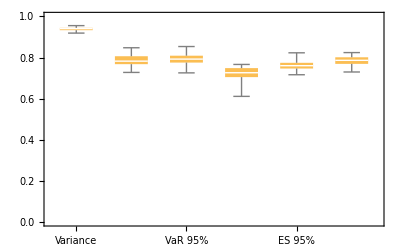

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

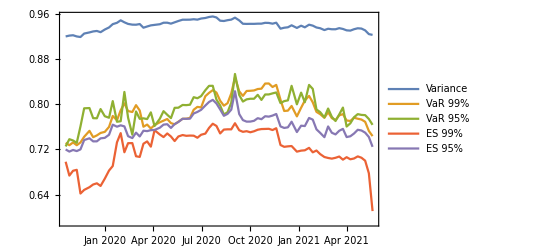

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

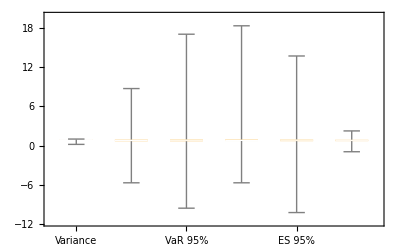

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

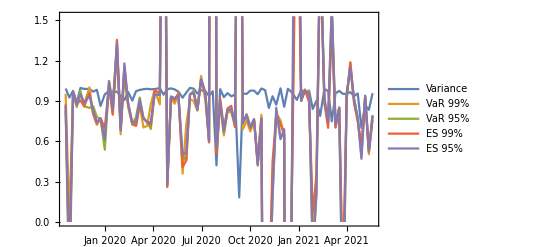

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,8]]
```

log return BITX

```mathematica
data[[1,7]]
```

log return future

```mathematica
data[[2,2]]
```

2019-10-18 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITX Price | % Change | log return future | log return BITX
405 | 2019-10-18 20:00:00+00:00 | 7990. | BTCX19 Curncy | 8334.07 | -1.37% | -0.0142904 | -0.0137695
406 | 2019-10-17 20:00:00+00:00 | 8105. | BTCX19 Curncy | 8449.62 | 1.80% | 0.0142904 | 0.017819
407 | 2019-10-16 20:00:00+00:00 | 7990. | BTCX19 Curncy | 8300.39 | -2.73% | -0.0295953 | -0.0276432
408 | 2019-10-15 20:00:00+00:00 | 8230. | BTCX19 Curncy | 8533.04 | -2.16% | -0.0222298 | -0.0218501
409 | 2019-10-14 20:00:00+00:00 | 8415. | BTCX19 Curncy | 8721.54 | -0.61% | 0. | 0.00710074
410 | 2019-10-11 20:00:00+00:00 | 8415. | BTCX19 Curncy | 8659.83 | -2.90% | -0.0275435 | -0.0294293
411 | 2019-10-10 20:00:00+00:00 | 8650. | BTCX19 Curncy | 8918.47 | -0.56% | -0.00403808 | -0.00562414
412 | 2019-10-09 20:00:00+00:00 | 8685. | BTCX19 Curncy | 8968.77 | 5.21% | 0.0544191 | 0.0507995
413 | 2019-10-08 20:00:00+00:00 | 8225. | BTCX19 Curncy | 8524.54 | -0.80% | -0.00787167 | -0.00801282)

```mathematica
hvec
```

{{2019-10-18},{0.962829},{0.912734},{0.984377},{0.957152},{0.963754},{0.961325},{{0.04229879682153612, {h$164529000 -> 0.9127338135362917}},{0.02227919701866284, {h$164529000 -> 0.9843770966290144}},{0.05512837718937894, {h$164529000 -> 0.9571521980028405}},{0.0349208151258406, {h$164529000 -> 0.9637536133214145}},{0.020430093342983853, {h$164529000 -> 0.9613246441365301}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

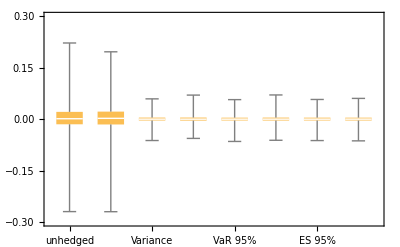

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

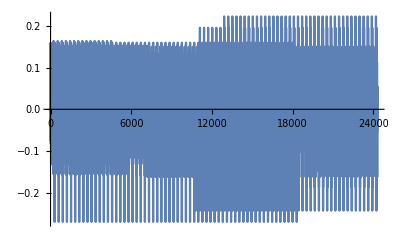

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

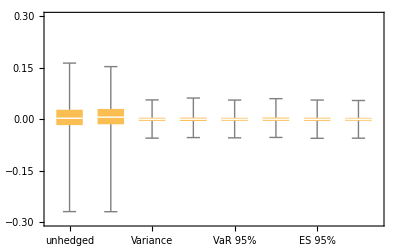

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

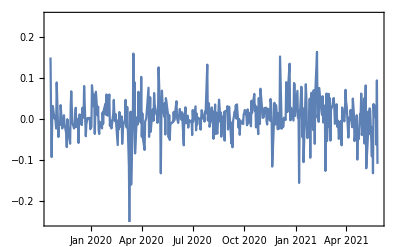
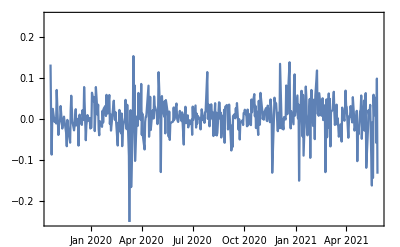

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

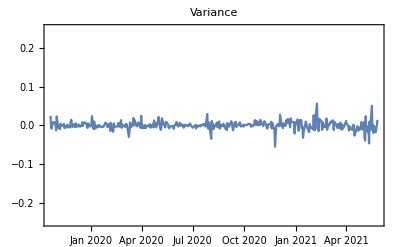
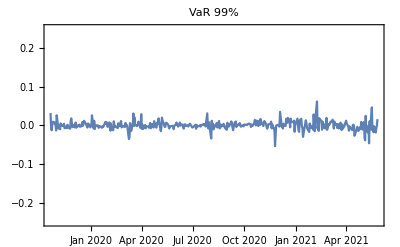
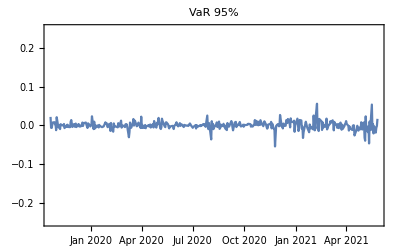
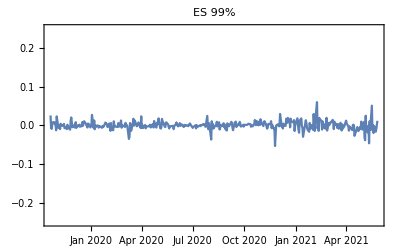
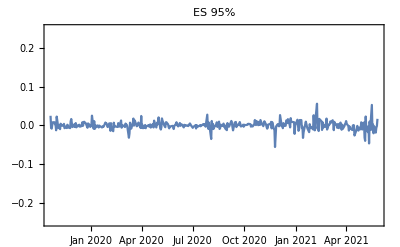
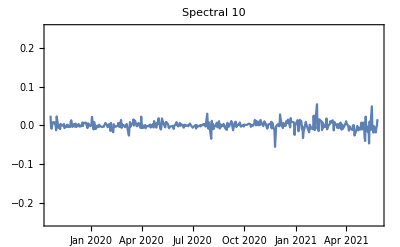

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

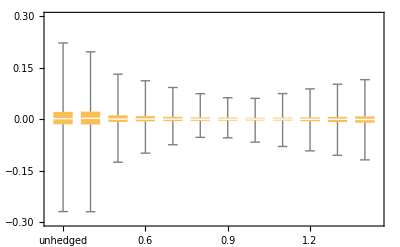

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

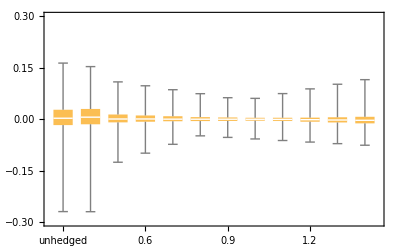

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤80, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.944558 | 0.959321 | 0.966204 | 0.92458 | 0.966204 | 0.958414
2021-05-13 | 0.928239 | 0.898045 | 0.949551 | 0.929819 | 0.943235 | 0.917029
2021-05-06 | 0.933594 | 0.915994 | 0.947216 | 0.913103 | 0.947216 | 0.950876
2021-04-29 | 0.939927 | 0.926126 | 0.947748 | 0.923164 | 0.953864 | 0.958908
2021-04-22 | 0.941089 | 0.929749 | 0.948091 | 0.919596 | 0.950669 | 0.967881
2021-04-15 | 0.941567 | 0.926363 | 0.953283 | 0.919336 | 0.949713 | 0.949666
2021-04-08 | 0.940246 | 0.919759 | 0.96035 | 0.919759 | 0.947319 | 0.952961
2021-04-01 | 0.940803 | 0.919069 | 0.964545 | 0.929534 | 0.953391 | 0.934804
2021-03-25 | 0.942623 | 0.921441 | 0.952227 | 0.917665 | 0.95088 | 0.964539
2021-03-18 | 0.945626 | 0.932708 | 0.949534 | 0.91313 | 0.949287 | 0.949564
2021-03-11 | 0.942914 | 0.926368 | 0.948027 | 0.926061 | 0.945106 | 0.947204
2021-03-04 | 0.942515 | 0.883871 | 0.953824 | 0.906725 | 0.946556 | 0.954543
2021-02-25 | 0.942408 | 0.934694 | 0.960573 | 0.890674 | 0.952403 | 0.961911
2021-02-18 | 0.94123 | 0.91029 | 0.949367 | 0.906571 | 0.947627 | 0.94235
2021-02-10 | 0.943991 | 0.922542 | 0.952001 | 0.912351 | 0.950133 | 0.969494
2021-02-03 | 0.954439 | 0.908001 | 0.95792 | 0.923369 | 0.957775 | 0.968424
2021-01-27 | 0.957178 | 0.913362 | 0.972749 | 0.889451 | 0.958092 | 0.98179
2021-01-20 | 0.958236 | 0.926353 | 0.975169 | 0.895113 | 0.959425 | 0.986841
2021-01-12 | 0.956351 | 0.916992 | 0.960827 | 0.913692 | 0.958353 | 0.964269
2021-01-05 | 0.955182 | 0.914168 | 0.973482 | 0.898151 | 0.960587 | 0.994946
2020-12-28 | 0.945555 | 0.908315 | 0.90918 | 0.892033 | 0.954718 | 0.978816
2020-12-18 | 0.945813 | 0.904178 | 0.933585 | 0.899057 | 0.958501 | 0.967335
2020-12-11 | 0.947152 | 0.899057 | 0.947523 | 0.899057 | 0.955883 | 0.977324
2020-12-04 | 0.947048 | 0.8988 | 0.909263 | 0.897608 | 0.955883 | 0.977596
2020-11-27 | 0.949797 | 0.895674 | 0.954557 | 0.935331 | 0.956978 | 0.944196
2020-11-19 | 0.948652 | 0.911879 | 0.928268 | 0.903331 | 0.959005 | 0.950494
2020-11-12 | 0.947621 | 0.937125 | 0.959715 | 0.90129 | 0.95868 | 0.953951
2020-11-05 | 0.945654 | 0.918774 | 0.959284 | 0.93369 | 0.952753 | 0.959383
2020-10-29 | 0.946729 | 0.91146 | 0.959338 | 0.923897 | 0.953392 | 0.948805
2020-10-22 | 0.946315 | 0.908644 | 0.948564 | 0.947578 | 0.955883 | 0.949744
2020-10-15 | 0.944809 | 0.906112 | 0.963213 | 0.947494 | 0.955883 | 0.921755
2020-10-08 | 0.941324 | 0.899308 | 0.955883 | 0.942085 | 0.954959 | 0.924476
2020-10-01 | 0.939636 | 0.900072 | 0.955883 | 0.937117 | 0.954771 | 0.93033
2020-09-24 | 0.938438 | 0.899155 | 0.956256 | 0.939262 | 0.954718 | 0.924044
2020-09-17 | 0.937967 | 0.894506 | 0.956657 | 0.964428 | 0.952347 | 0.92779
2020-09-10 | 0.939729 | 0.907247 | 0.947454 | 0.922559 | 0.955674 | 0.932113
2020-09-02 | 0.930194 | 0.921513 | 0.934183 | 0.907239 | 0.938542 | 0.935477
2020-08-26 | 0.917327 | 0.894366 | 0.916862 | 0.949412 | 0.922292 | 0.904218
2020-08-19 | 0.91501 | 0.90421 | 0.90679 | 0.95955 | 0.926636 | 0.901483
2020-08-12 | 0.913274 | 0.887677 | 0.924238 | 0.964994 | 0.929388 | 0.902899
2020-08-05 | 0.914327 | 0.898315 | 0.917147 | 0.951667 | 0.924019 | 0.918043
2020-07-29 | 0.918498 | 0.892836 | 0.954328 | 0.963075 | 0.925931 | 0.909681
2020-07-22 | 0.923861 | 0.908894 | 0.957367 | 0.964869 | 0.937945 | 0.915916
2020-07-15 | 0.919258 | 0.891245 | 0.933903 | 0.888797 | 0.917134 | 0.925514
2020-07-08 | 0.918212 | 0.887539 | 0.942389 | 0.939936 | 0.926249 | 0.909148
2020-06-30 | 0.918435 | 0.890232 | 0.924402 | 0.935465 | 0.927035 | 0.915498
2020-06-23 | 0.917012 | 0.875829 | 0.926636 | 0.93385 | 0.928564 | 0.917928
2020-06-16 | 0.918697 | 0.874049 | 0.947963 | 0.92838 | 0.933217 | 0.919806
2020-06-09 | 0.925803 | 0.885947 | 0.956132 | 0.956551 | 0.940259 | 0.927917
2020-06-02 | 0.926122 | 0.883729 | 0.956077 | 0.956451 | 0.940295 | 0.932762
2020-05-26 | 0.926153 | 0.959084 | 0.941701 | 0.952556 | 0.940295 | 0.933006
2020-05-18 | 0.924952 | 0.955511 | 0.944146 | 0.953661 | 0.937798 | 0.917975
2020-05-11 | 0.924429 | 0.971086 | 0.943973 | 0.949388 | 0.938144 | 0.929225
2020-05-04 | 0.924861 | 0.897162 | 0.944033 | 0.953078 | 0.932528 | 0.932897
2020-04-27 | 0.929742 | 0.958996 | 0.948502 | 0.958996 | 0.937379 | 0.956302
2020-04-20 | 0.930095 | 0.961587 | 0.956629 | 0.955458 | 0.938243 | 0.960562
2020-04-13 | 0.929826 | 0.866172 | 0.939871 | 0.948751 | 0.935707 | 0.943691
2020-04-03 | 0.929925 | 0.968965 | 0.933598 | 0.964588 | 0.931911 | 0.951709
2020-03-27 | 0.931637 | 0.88374 | 0.957779 | 0.946404 | 0.937853 | 0.957886
2020-03-20 | 0.930787 | 0.899104 | 0.937067 | 0.932056 | 0.935029 | 0.949383
2020-03-13 | 0.928479 | 0.855209 | 0.943365 | 0.938942 | 0.936206 | 0.950619
2020-03-06 | 0.934388 | 0.870673 | 0.925213 | 0.875579 | 0.910847 | 0.973726
2020-02-28 | 0.937214 | 0.866684 | 0.940925 | 0.864899 | 0.901176 | 0.983564
2020-02-21 | 0.939745 | 0.870451 | 0.902457 | 0.91644 | 0.914532 | 0.955782
2020-02-13 | 0.93976 | 0.869142 | 0.900671 | 0.911357 | 0.915222 | 0.964768
2020-02-06 | 0.943076 | 0.817458 | 0.935394 | 0.817491 | 0.895545 | 0.980789
2020-01-30 | 0.946358 | 0.895313 | 0.956604 | 0.942817 | 0.934594 | 0.962202
2020-01-23 | 0.941635 | 0.883686 | 0.919021 | 0.939168 | 0.934893 | 0.966538
2020-01-15 | 0.940886 | 0.871035 | 0.955213 | 0.864349 | 0.906902 | 0.963812
2020-01-08 | 0.93702 | 0.874225 | 0.917282 | 0.897162 | 0.913446 | 0.961333
2019-12-31 | 0.936746 | 0.900175 | 0.941112 | 0.884474 | 0.915544 | 0.959815
2019-12-23 | 0.934551 | 0.84283 | 0.951512 | 0.833652 | 0.896753 | 0.97809
2019-12-16 | 0.93791 | 0.889529 | 0.962394 | 0.902655 | 0.919391 | 0.953775
2019-12-09 | 0.937534 | 0.888895 | 0.957335 | 0.89739 | 0.919439 | 0.95611
2019-12-02 | 0.940121 | 0.849727 | 0.959725 | 0.814835 | 0.907835 | 0.971005
2019-11-22 | 0.947783 | 0.885675 | 0.959695 | 0.843443 | 0.914879 | 0.969062
2019-11-15 | 0.946331 | 0.913484 | 0.968428 | 0.876336 | 0.920372 | 0.970653
2019-11-08 | 0.949409 | 0.910716 | 0.984001 | 0.934765 | 0.9413 | 0.964558
2019-11-01 | 0.951718 | 0.913484 | 0.982515 | 0.951066 | 0.942553 | 0.961685
2019-10-25 | 0.953604 | 0.910716 | 0.981178 | 0.952389 | 0.959058 | 0.953977
2019-10-18 | 0.962829 | 0.912734 | 0.984377 | 0.957152 | 0.963754 | 0.961325)

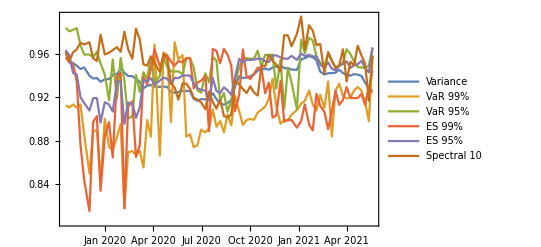

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```